# Harmonický ustálený stav (HUS), přenos, časová oblast , stejnosměrný stav

-Graphics-
Vstupní napětí  uZ[t]má sinusový průběh o frekvenci f=100 Hz.Fázor vstupního napětí má hodnotu Û=3+6j. Hodnoty součástek jsou následující:
R1=10 kΩ,
R2=10 kΩ,
R3=10 kΩ,
C2=10 nF,
L1=10 mH.
Řešte obvod metodou uzlových napětí v časové oblasti. Zobrazte napětí uout[t] společně se zdrojovým napětím uZ[t].

### PODROBNÉ řešení příkladu v časové oblasti

-Graphics-

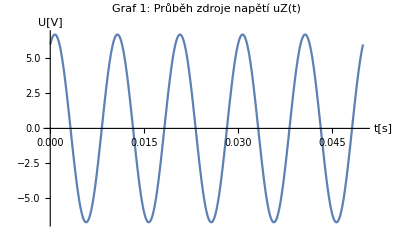

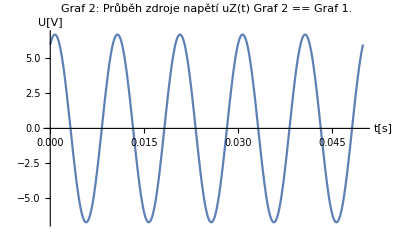

{{iUz[t]→InterpolatingFunction[…][t],iR1[t]→InterpolatingFunction[…][t],iR2[t]→InterpolatingFunction[…][t],iR3[t]→InterpolatingFunction[…][t],iL1[t]→InterpolatingFunction[…][t],iC2[t]→InterpolatingFunction[…][t],u1[t]→InterpolatingFunction[…][t],u2[t]→InterpolatingFunction[…][t],u3[t]→InterpolatingFunction[…][t]}}

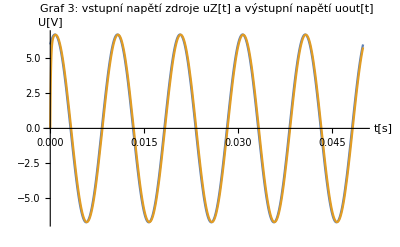

Všimněte si, že křivka u3[t] začíná přesně v 0, podívejte se na tento příklad řešený v HUSu.

```mathematica
ClearAll["Global`*"]

(* Definice zdroje napětí *)
uZ = 3+6*ⅉ;
frekvence  = 100;
perioda = 1/frekvence;
tmax = 5*perioda;
tmax1 =0.3;

(* Převedu si zdroj napětí z fázoru do časové oblasti, abych se mohl podívat jak vypadá *)
φ = Arg[uZ];
amplituda= Abs[uZ];
omega = {ω->2*π*frekvence};
(* Definice funkce pro zdroj napětí v časové oblasti *)
uZ1[t_]:=amplituda*Sin[2*π*frekvence*t+φ]
uZ2[t_]:=amplituda*Im[ⅇ^(ⅉ*ω*t+ⅉ*φ)]/.omega

Plot[uZ1[t],{t,0,tmax}, AxesLabel->{"t[s]","U[V]"}, PlotLabel->"Graf 1: Průběh zdroje napětí uZ(t)"] (* tímto si ověřím, že zadefinovaný zdroj napětí, který jsem si převedl do časové oblasti je správný - že půjde vykreslit a bude mít požadovanou amplitudu, posun a frekvenci*)
Plot[uZ2[t],{t,0,tmax}, AxesLabel->{"t[s]","U[V]"}, PlotLabel->"Graf 2: Průběh zdroje napětí uZ(t) Graf 2 == Graf 1."](* tímto si ověřím další možný způsob převodu zadefinovaného zdroje napětí, který jsem si převedl do časové oblasti je správný - že půjde vykreslit a bude mít požadovanou amplitudu, posun a frekvenci, pod sebou bych měl vidět dva stejné grafy *)

soucastky={
R1-> 10*10^3,
R2->10*10^3,
R3->10*10^3,
L1->10*10^-3,
C2->10*10^-9
};

rovnice = {
iUz[t]==iR1[t]+iL1[t], (* uzel 1 *)
iR1[t]+iL1[t]==iR3[t]+iR2[t],(* uzel 2 *)
iR2[t]==iC2[t], (* uzel 3 *)

(* rovnice pro součástky *)
uZ1[t]==u1[t],
u1[t]-u2[t]==R1*iR1[t],
u2[t]-u3[t]==R2*iR2[t],
u2[t]==R3*iR3[t],
u1[t]-u2[t]==L1*iL1'[t],
C2*u3'[t]==iC2[t],

(* počáteční podmínky *)
iL1[0]==0,
u3[0]==0
};

nezname={
iUz[t],
iR1[t],iR2[t],iR3[t],
iL1[t],
iC2[t],
u1[t],u2[t],u3[t]
};

reseni = NDSolve[rovnice/.soucastky, nezname,{t,0,tmax}, StartingStepSize->10^-9]
Plot[{uZ1[t],u3[t]/.reseni},{t,0,tmax}, AxesLabel->{"t[s]","U[V]"}, PlotLabel->"Graf 3: vstupní napětí zdroje uZ[t] a výstupní napětí uout[t]"]
Print["Všimněte si, že křivka u3[t] začíná přesně v 0, podívejte se na tento příklad řešený v HUSu. "]
```